```mathematica
SetOptions[EvaluationNotebook[],PrintPrecision->8]
```

## Aufgabe 3

```mathematica
data30=309.2
```

309.2

```mathematica
data3={{291.5,266.5},{328.8,351.3}}
```

{{291.5,266.5},{328.8,351.3}}

```mathematica
data3processed=Table[(data3[[2,i]]-data3[[1,i]])/2,{i,1,2}]
```

{18.65,42.4}

```mathematica
(0.1)/Sqrt[2]
```

0.0707107

```mathematica
data3radians=data3processed*2Pi/360
```

{0.325504,0.74002}

```mathematica
data3processed Degree
```

{0.325504,0.74002}

```mathematica
0.1/(√2) *2Pi/360
```

0.00123413

```mathematica
data3sines=Sin[#]&/@data3radians
```

{0.319786,0.674302}

```mathematica
data3sineserror=Cos[#]*0.1/(√2) *2Pi/360&/@data3radians
```

{0.00116933,0.000911353}

```mathematica
data3sines/(0.1/40)
```

{127.915,269.721}

```mathematica
data3sineserror/(0.1/40)
```

{0.467732,0.364541}

```mathematica
data3sines[[2]]-data3sines[[1]]
```

0.354516

```mathematica
√Total[(#1^2&)/@data3sineserror]
```

0.00148253

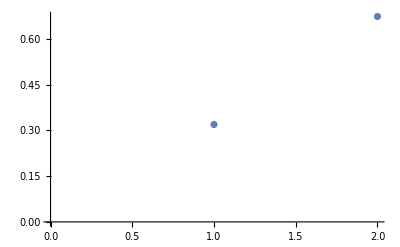

```mathematica
ListPlot[Sin[# Degree]&/@data3processed]
```

```mathematica
Sin[data3processed[[2]]Degree]-Sin[data3processed[[1]]Degree]
```

0.354516

```mathematica
328.8-309.2
```

19.6

```mathematica
309.2-291.5
```

17.7

```mathematica
351.3-309.2
```

42.1

```mathematica
309.2-266.5
```

42.7

## Aufgabe 5

```mathematica
data50=126.3
data5={{71.8,86.4,97.3,91.3},{172.1,164.0,155.6,160.9}}
```

126.3

{{71.8,86.4,97.3,91.3},{172.1,164.,155.6,160.9}}

## Aufgabe 7

```mathematica
cf=ColorData["VisibleSpectrum"]
```

ColorDataFunction[…]

```mathematica
wavelengths={643.9,579.1,546.1,508.6,480.0,467.8,435.8,404.7}
```

{643.9,579.1,546.1,508.6,480.,467.8,435.8,404.7}

```mathematica
cf/@wavelengths
```

{RGBColor[0.9672897238016622, 0., 0.],RGBColor[1., 0.9258482539075773, 0.],RGBColor[0., 1., 0.],RGBColor[0., 0.9743380178113661, 0.4033040430876886],RGBColor[0., 0.48449418286510887, 1.],RGBColor[0., 0.09872836549392221, 1.],RGBColor[0.47842342393879017, 0., 1.],RGBColor[0.23437896046341472, 0., 0.4939999999999998]}

```mathematica
schwerflintglas={138.0,138.8,139.3,140.2,140.8,141.3,142.5,144.2}-79.1
```

{58.9,59.7,60.2,61.1,61.7,62.2,63.4,65.1}

```mathematica
schwerflintglasint=Interpolation[Transpose[{wavelengths,schwerflintglas}],InterpolationOrder->Automatic]
```

InterpolatingFunction[…]

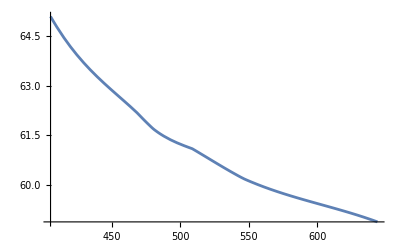

```mathematica
Plot[schwerflintglasint[x],{x,405,644}]
```

## Aufgabe 10.1

```mathematica
data10={140.6,139.9,142.2}-81.0
```

{59.6,58.9,61.2}

```mathematica
Values[Solve[schwerflintglasint[x]==#1,x]]&/@data10
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve::ifun will be suppressed during this calculation.

{{{587.228}},{{643.9}},{{502.079}}}

```mathematica
FindRoot[schwerflintglas[x]-data10[[1]],{x,500}]
```

FindRoot::nlnum: The function value {-59.6+{58.9,59.7,60.2,61.1,61.7,62.2,63.4,65.1}[500.]} is not a list of numbers with dimensions {1} at {x} = {500.}.

FindRoot[schwerflintglas[x]-data10⟦1⟧,{x,500}]

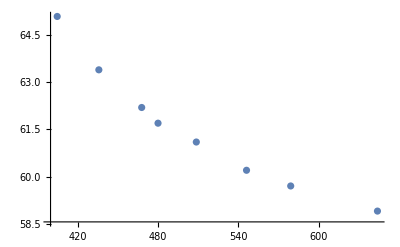

```mathematica
ListPlot[]
```

```mathematica
140-81
```

59

```mathematica
59+79.1
```

138.1